# QEA - Differential Equations

```mathematica
SetDirectory@NotebookDirectory[];
<<"../General.m"
```

## Linear Equations Example 2

```mathematica
With[{context="linearequationsexample2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{},
sol=DSolveValue[{v'[t]==9.8-.196v[t]},v[t],t]
]
```

50.+ⅇ^(-0.196 t) C[1]

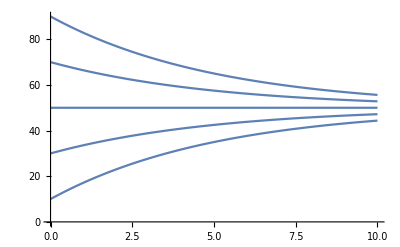

```mathematica
Plot[Table[sol/.C[1]-> v0,{v0,{Range[-40,40,20]}}],{t,0,10},PlotRange->{{0,10},{0,90}}]
```

```mathematica
With[{context="linearequationsexample2`"},If[Context[]==context,End[],"Not in context"]]
```

linearequationsexample2`

## Linear Equations Example 3

```mathematica
With[{context="linearequationsexample3`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{},
sol=DSolveValue[{Cos[x]y'[x]+Sin[x]y[x]==2 Cos[x]^3 Sin[x]-1,y[π/4]==3Sqrt[2]},y[x],x]
]
```

1/2 (14 Cos[x]-Cos[x] Cos[2 x]-2 Sin[x])

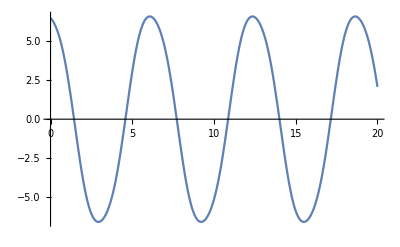

```mathematica
Plot[sol,{x,0,20}]
```

```mathematica
With[{context="linearequationsexample3`"},If[Context[]==context,End[],"Not in context"]]
```

linearequationsexample3`

## Linear Equations Example 4

```mathematica
With[{context="linearequationsexample4`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{
de={t y'[t]+2y[t]==t^2-t+1},
initialConditions={y[1]==1/2}
},
sol=DSolveValue[Join[de,initialConditions],y[t],t]
]
```

(1+6 t^2-4 t^3+3 t^4)/(12 t^2)

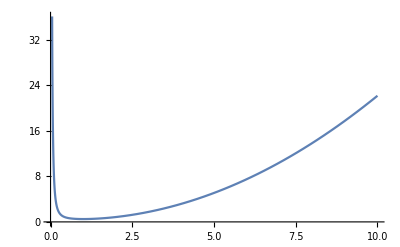

```mathematica
Plot[sol,{t,0,10}]
```

```mathematica
With[{context="linearequationsexample4`"},If[Context[]==context,End[],"Not in context"]]
```

linearequationsexample4`

## Separable Equations Example 1

```mathematica
With[{context="separableequationsexample1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{
de={y'[x]==6 y[x]^2 x},
initialConditions={y[1]==1/25}
},
sol=DSolveValue[Join[de,initialConditions],y[x],x]
]
```

1/(28-3 x^2)

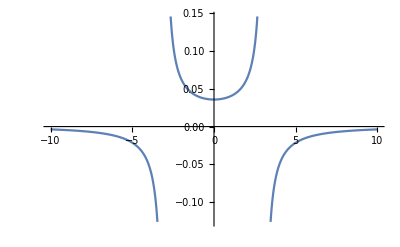

```mathematica
Plot[sol,{x,-10,10}]
```

```mathematica
With[{context="separableequationsexample1`"},If[Context[]==context,End[],"Not in context"]]
```

separableequationsexample1`

```mathematica
makeTemplate["Separable Equations Example 2"]
```

## Separable Equations Example 2

```mathematica
With[{context="separableequationsexample2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{
de={y'[x]==(3 x^2+4x-4)/(2y[x]-4)},
initialConditions={y[1]==3}
},
sol=DSolveValue[Join[de,initialConditions],y[x],x]
]
```

DSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

2+√(2-4 x+2 x^2+x^3)

```mathematica
sol/.x->-5
```

2+ⅈ √53

```mathematica
Reduce[2+√(2-4 x+2 x^2+x^3)>=0,x]
```

x≥Root[2-4 #1+2 #1^2+#1^3&,1]

```mathematica
sol
```

2+√(2-4 x+2 x^2+x^3)

```mathematica
Solve[2+√(2-4 x+2 x^2+x^3)==0,x]
```

{}

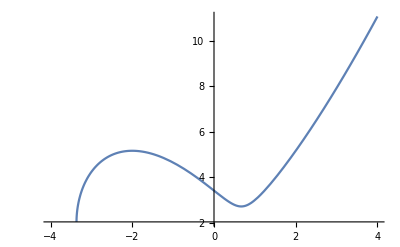

```mathematica
Plot[sol,{x,-4,4}]
```

```mathematica
With[{context="separableequationsexample2`"},If[Context[]==context,End[],"Not in context"]]
```

separableequationsexample2`

## Separable Equations Example 3

```mathematica
With[{context="separableequationsexample3`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{
de={y'[x]==(x y[x]^3)/Sqrt[1+x^2]},
initialConditions={y[0]==-1}
},
sol=DSolveValue[Join[de,initialConditions],y[x],x]
]
```

DSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

-1/(√(3-2 √(1+x^2)))

```mathematica
validity=Solve[Denominator[sol]==0,x]
```

{{x→-(√5)/2},{x→(√5)/2}}

```mathematica
x/.validity
```

{-(√5)/2,(√5)/2}

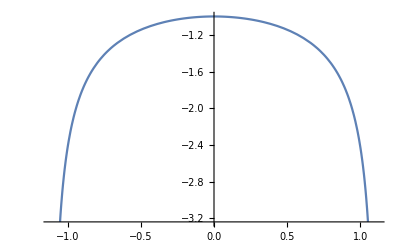

```mathematica
Plot[sol,{x,-(√5)/2,(√5)/2}]
```

```mathematica
With[{context="separableequationsexample3`"},If[Context[]==context,End[],"Not in context"]]
```

separableequationsexample3`

## Separable Equations Example 4

```mathematica
With[{context="separableequationsexample4`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{
de={y'[x]==ⅇ^(-y[x])(2x-4)},
initialConditions={y[5]==0}
},
sol=DSolveValue[Join[de,initialConditions],y[x],x]
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Log[-4+2 (-2 x+x^2/2)]

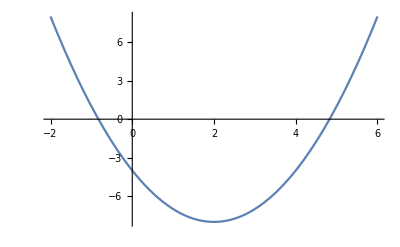

```mathematica
Plot[-4+2 (-2 x+x^2/2),{x,-2,6}]
```

```mathematica
validity=Solve[-4+2 (-2 x+x^2/2)==0,x];
x/.validity
```

{2 (1-√2),2 (1+√2)}

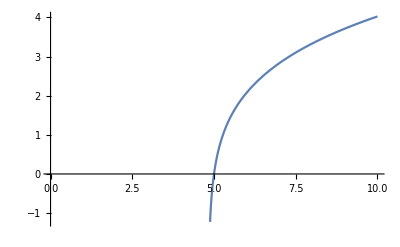

```mathematica
Plot[sol,{x,0,10}]
```

```mathematica
With[{context="separableequationsexample4`"},If[Context[]==context,End[],"Not in context"]]
```

separableequationsexample4`

## Separable Equations Example 5

```mathematica
With[{context="separableequationsexample5`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{
de={r'[θ]==r[θ]^2/θ},
initialConditions={r[1]==2}
},
sol=DSolveValue[Join[de,initialConditions],r[θ],θ]
]
```

-2/(-1+2 Log[θ])

```mathematica
Denominator[-2/(-1+2 Log[θ])]
```

-1+2 Log[θ]

```mathematica
Solve[-1+2 Log[θ]==0,θ]
```

{{θ→√ⅇ}}

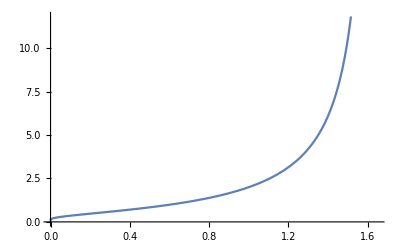

```mathematica
Plot[sol,{θ,0,Sqrt[ⅇ]}]
```

```mathematica
With[{context="separableequationsexample5`"},If[Context[]==context,End[],"Not in context"]]
```

separableequationsexample5`

## Modeling Example 1

```mathematica
With[{context="modelingexample1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{
de={q'[t]==9/5(1+Cos[t])-(2q[t])/(200+t)},
initialConditions={q[0]==5}
},
sol=DSolveValue[Join[de,initialConditions],q[t],t]
]
```

1/(5 (200+t)^2)(996400+360000 t+1800 t^2+3 t^3+3600 Cos[t]+18 t Cos[t]+359982 Sin[t]+3600 t Sin[t]+9 t^2 Sin[t])

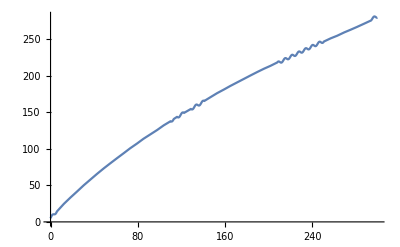

```mathematica
Plot[sol,{t,0,300}]
```

```mathematica
With[{context="modelingexample1`"},If[Context[]==context,End[],"Not in context"]]
```

modelingexample1`

```mathematica
exportNotebookPDF[]
```

/home/nathan/olin/fall2016/qEAFall2016Homework/attitudeControl/differentialEquations/differentialEquations.pdf